

```mathematica
JacobsThalGraph2[3]
```

```mathematica
Summ[assoc_]:=Table[k->Length[assoc[k]],{k,Sort[Keys[assoc]]}]
```

```mathematica
Table[ChromaticPolynomial[JacobsThalGraph2[k],4]/24,{k,3,12}]
```

{1,1,1,4,5,12,21,44,85,172}

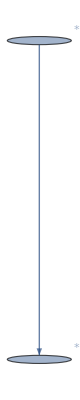
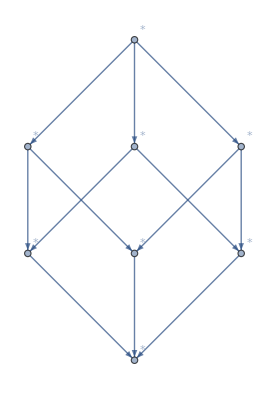
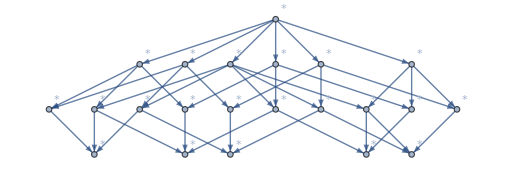
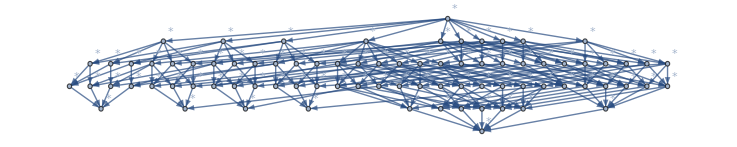

```mathematica
Table[With[
{help=FormulaGraph[FindFullFormula[JacobsThalGraph2[k]]]},
Graph[EdgeList[help],VertexLabels->Table[v->Tooltip["*",v],{v,VertexList[help]}],GraphLayout->"LayeredDigraphEmbedding"]
],{k,5,8}]
```

```mathematica
TableForm[Table[Summ[BaseGenerators[FindFullFormula[JacobsThalGraph2[k]]]],{k,3,12}]]
```

```mathematica
VertexList[FormulaGraph[FindFullFormula[JacobsThalGraph2[8]]]]
```

{v168x257x34,v168x257x3x4,v168x25x34x7,v168x25x3x4x7,v168x27x34x5,v168x27x3x4x5,v168x2x34x57,v168x2x34x5x7,v168x2x3x4x57,v168x2x3x4x5x7,v16x257x34x8,v16x257x3x4x8,v16x25x34x7x8,v16x25x3x4x7x8,v16x27x34x58,v16x27x34x5x8,v16x27x3x4x58,v16x27x3x4x5x8,v16x2x34x57x8,v16x2x34x58x7,v16x2x34x5x7x8,v16x2x3x4x57x8,v16x2x3x4x58x7,v16x2x3x4x5x7x8,v17x25x34x68,v17x25x34x6x8,v17x25x3x4x68,v17x25x3x4x6x8,v17x26x34x58,v17x26x34x5x8,v17x26x3x4x58,v17x26x3x4x5x8,v17x2x34x58x6,v17x2x34x5x68,v17x2x34x5x6x8,v17x2x3x4x58x6,v17x2x3x4x5x68,v17x2x3x4x5x6x8,v18x257x34x6,v18x257x3x4x6,v18x25x34x6x7,v18x25x3x4x6x7,v18x26x34x57,v18x26x34x5x7,v18x26x3x4x57,v18x26x3x4x5x7,v18x27x34x5x6,v18x27x3x4x5x6,v18x2x34x57x6,v18x2x34x5x6x7,v18x2x3x4x57x6,v18x2x3x4x5x6x7,v1x257x34x68,v1x257x34x6x8,v1x257x3x4x68,v1x257x3x4x6x8,v1x25x34x68x7,v1x25x34x6x7x8,v1x25x3x4x68x7,v1x25x3x4x6x7x8,v1x26x34x57x8,v1x26x34x58x7,v1x26x34x5x7x8,v1x26x3x4x57x8,v1x26x3x4x58x7,v1x26x3x4x5x7x8,v1x27x34x58x6,v1x27x34x5x68,v1x27x34x5x6x8,v1x27x3x4x58x6,v1x27x3x4x5x68,v1x27x3x4x5x6x8,v1x2x34x57x68,v1x2x34x57x6x8,v1x2x34x58x6x7,v1x2x34x5x68x7,v1x2x34x5x6x7x8,v1x2x3x4x57x68,v1x2x3x4x57x6x8,v1x2x3x4x58x6x7,v1x2x3x4x5x68x7,v1x2x3x4x5x6x7x8}

```mathematica
edges=EdgeList[FormulaGraph[FindFullFormula[JacobsThalGraph2[8]]]];
```

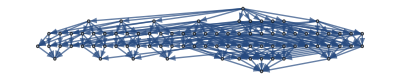
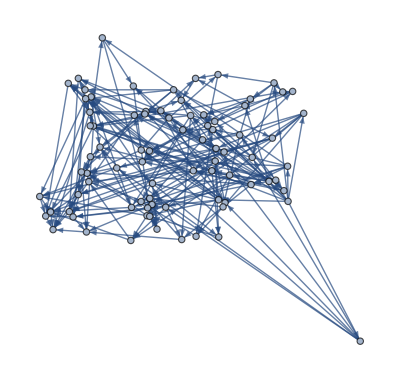
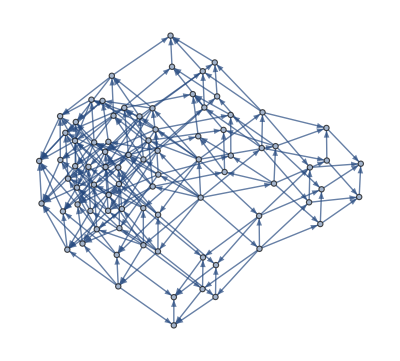
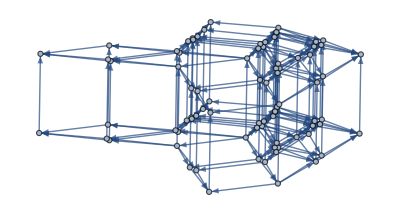
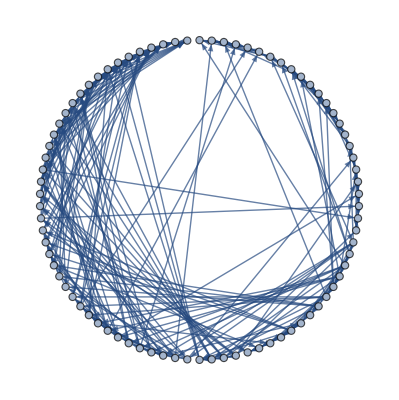
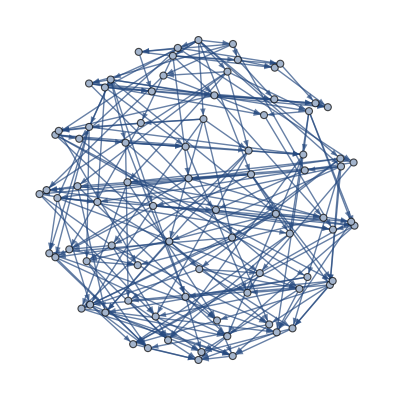
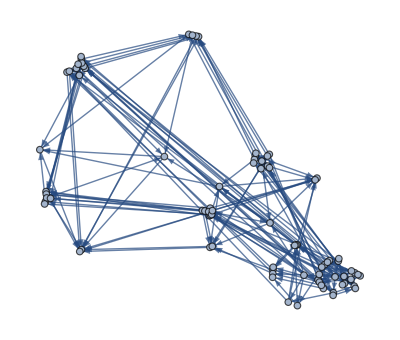
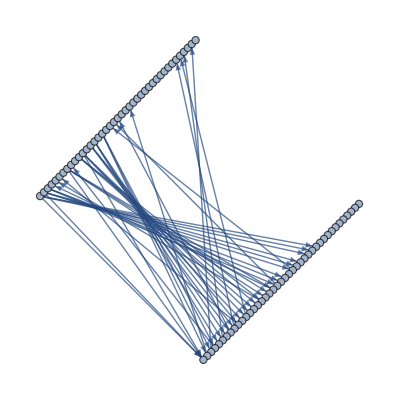

```mathematica
Table[Graph[edges,GraphLayout->layout],{layout,{"LayeredDigraphEmbedding","SpringEmbedding","SpringElectricalEmbedding","HighDimensionalEmbedding","CircularEmbedding","SpiralEmbedding","BalloonEmbedding","BipartiteEmbedding","CircularMultipartiteEmbedding","DiscreteSpiralEmbedding","GridEmbedding","LinearEmbedding","MultipartiteEmbedding","StarEmbedding","RadialEmbedding","LayeredEmbedding"}}]
```

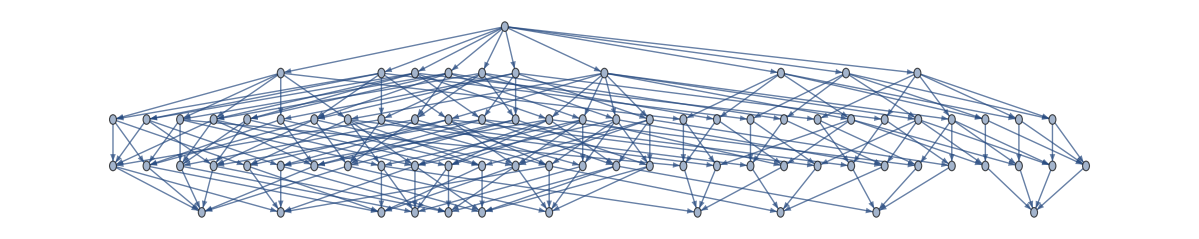

```mathematica
VertexDelete[-Graphics-,v168x257x34]
```

## Hello how

```mathematica
SymbolRank[s_]:=StringCount[SymbolName[s],"x"]+1
```

```mathematica
SymbolRank[v1234x5]
```

0

```mathematica
Table[With[
{help=FindFullFormula[JacobsThalGraph2[k]]},
Map[Last,Sort[Tally[Map[SymbolRank[#]&,help]]]]
],{k,5,14,2}]//TableForm
```

1 | 1 |  |  |  |  |  |  |  | 
5 | 10 | 6 | 1 |  |  |  |  |  | 
21 | 91 | 126 | 70 | 15 | 1 |  |  |  | 
85 | 820 | 2142 | 2331 | 1170 | 273 | 28 | 1 |  | 
341 | 7381 | 34782 | 64240 | 56925 | 25872 | 6160 | 759 | 45 | 1